```mathematica
Subscript[ϵ, r]=D[u[r,θ],r];
Subscript[ϵ, θ]=u/r+D[v[r,θ],θ]/r;
Subscript[γ, rθ]=D[u[r,θ],θ]/r+D[v[r,θ],r]-v/r;
Subscript[σ, r]=(Eu/(1-ν^2))*(Subscript[ϵ, r]+ν*Subscript[ϵ, θ]);
Subscript[σ, θ]=(Eu/(1-ν^2))*(Subscript[ϵ, θ]+ν*Subscript[ϵ, r]);
Subscript[GU0σ, r]=Simplify[Subscript[σ, r]/.D[u[r,θ],{θ,2}]->((Subscript[y, n,m+1]-2*Subscript[y, n,m]+Subscript[y, n,m-1])/τ^2)/.
D[u[r,θ],{r,2}]->((Subscript[y, n+1,m]-2*Subscript[y, n,m]+Subscript[y, n-1,m])/h^2)/.
D[u[r,θ],{r,1}]->((Subscript[y, n+1,m]-Subscript[y, n-1,m])/(2*h))/. D[u[r,θ],{θ,1}]->((Subscript[y, n,m+1]-Subscript[y, n,m-1])/(2*τ))/.
D[D[u[r,θ],{r,1}],θ]->((Subscript[y, n+1,m+1]-Subscript[y, n-1,m+1]-Subscript[y, n+1,m-1]+Subscript[y, n-1,m-1])/(4*h*τ))/.
D[v[r,θ],{θ,2}]->((Subscript[z, n,m+1]-2*Subscript[z, n,m]+Subscript[z, n,m-1])/τ^2)/.
D[v[r,θ],{r,2}]->((Subscript[z, n+1,m]-2*Subscript[z, n,m]+Subscript[z, n-1,m])/h^2)/.
D[v[r,θ],{r,1}]->((Subscript[z, n+1,m]-Subscript[z, n-1,m])/(2*h))/. D[v[r,θ],{θ,1}]->((Subscript[z, n,m+1]-Subscript[z, n,m-1])/(2*τ))/.
D[D[v[r,θ],{r,1}],θ]->((Subscript[z, n+1,m+1]-Subscript[z, n-1,m+1]-Subscript[z, n+1,m-1]+Subscript[z, n-1,m-1])/(4*h*τ))/.
u[r,θ]->Subscript[y, n,m]/. v[r,θ]->Subscript[z, n,m]/.n->0]
Subscript[GU0σ, θ]=Simplify[Subscript[σ, r]/.D[u[r,θ],{θ,2}]->((Subscript[y, n,m+1]-2*Subscript[y, n,m]+Subscript[y, n,m-1])/τ^2)/.
D[u[r,θ],{r,2}]->((Subscript[y, n+1,m]-2*Subscript[y, n,m]+Subscript[y, n-1,m])/h^2)/.
D[u[r,θ],{r,1}]->((Subscript[y, n+1,m]-Subscript[y, n-1,m])/(2*h))/. D[u[r,θ],{θ,1}]->((Subscript[y, n,m+1]-Subscript[y, n,m-1])/(2*τ))/.
D[D[u[r,θ],{r,1}],θ]->((Subscript[y, n+1,m+1]-Subscript[y, n-1,m+1]-Subscript[y, n+1,m-1]+Subscript[y, n-1,m-1])/(4*h*τ))/.
D[v[r,θ],{θ,2}]->((Subscript[z, n,m+1]-2*Subscript[z, n,m]+Subscript[z, n,m-1])/τ^2)/.
D[v[r,θ],{r,2}]->((Subscript[z, n+1,m]-2*Subscript[z, n,m]+Subscript[z, n-1,m])/h^2)/.
D[v[r,θ],{r,1}]->((Subscript[z, n+1,m]-Subscript[z, n-1,m])/(2*h))/. D[v[r,θ],{θ,1}]->((Subscript[z, n,m+1]-Subscript[z, n,m-1])/(2*τ))/.
D[D[v[r,θ],{r,1}],θ]->((Subscript[z, n+1,m+1]-Subscript[z, n-1,m+1]-Subscript[z, n+1,m-1]+Subscript[z, n-1,m-1])/(4*h*τ))/.
u[r,θ]->Subscript[y, n,m]/. v[r,θ]->Subscript[z, n,m]/.n->0]
Subscript[GUMσ, r]=Simplify[Subscript[σ, r]/.D[u[r,θ],{θ,2}]->((Subscript[y, n,m+1]-2*Subscript[y, n,m]+Subscript[y, n,m-1])/τ^2)/.
D[u[r,θ],{r,2}]->((Subscript[y, n+1,m]-2*Subscript[y, n,m]+Subscript[y, n-1,m])/h^2)/.
D[u[r,θ],{r,1}]->((Subscript[y, n+1,m]-Subscript[y, n-1,m])/(2*h))/. D[u[r,θ],{θ,1}]->((Subscript[y, n,m+1]-Subscript[y, n,m-1])/(2*τ))/.
D[D[u[r,θ],{r,1}],θ]->((Subscript[y, n+1,m+1]-Subscript[y, n-1,m+1]-Subscript[y, n+1,m-1]+Subscript[y, n-1,m-1])/(4*h*τ))/.
D[v[r,θ],{θ,2}]->((Subscript[z, n,m+1]-2*Subscript[z, n,m]+Subscript[z, n,m-1])/τ^2)/.
D[v[r,θ],{r,2}]->((Subscript[z, n+1,m]-2*Subscript[z, n,m]+Subscript[z, n-1,m])/h^2)/.
D[v[r,θ],{r,1}]->((Subscript[z, n+1,m]-Subscript[z, n-1,m])/(2*h))/. D[v[r,θ],{θ,1}]->((Subscript[z, n,m+1]-Subscript[z, n,m-1])/(2*τ))/.
D[D[v[r,θ],{r,1}],θ]->((Subscript[z, n+1,m+1]-Subscript[z, n-1,m+1]-Subscript[z, n+1,m-1]+Subscript[z, n-1,m-1])/(4*h*τ))/.
u[r,θ]->Subscript[y, n,m]/. v[r,θ]->Subscript[z, n,m]/.n->(b-a)/h];
Subscript[GUMσ, θ]=Simplify[Subscript[σ, θ]/.D[u[r,θ],{θ,2}]->((Subscript[y, n,m+1]-2*Subscript[y, n,m]+Subscript[y, n,m-1])/τ^2)/.
D[u[r,θ],{r,2}]->((Subscript[y, n+1,m]-2*Subscript[y, n,m]+Subscript[y, n-1,m])/h^2)/.
D[u[r,θ],{r,1}]->((Subscript[y, n+1,m]-Subscript[y, n-1,m])/(2*h))/. D[u[r,θ],{θ,1}]->((Subscript[y, n,m+1]-Subscript[y, n,m-1])/(2*τ))/.
D[D[u[r,θ],{r,1}],θ]->((Subscript[y, n+1,m+1]-Subscript[y, n-1,m+1]-Subscript[y, n+1,m-1]+Subscript[y, n-1,m-1])/(4*h*τ))/.
D[v[r,θ],{θ,2}]->((Subscript[z, n,m+1]-2*Subscript[z, n,m]+Subscript[z, n,m-1])/τ^2)/.
D[v[r,θ],{r,2}]->((Subscript[z, n+1,m]-2*Subscript[z, n,m]+Subscript[z, n-1,m])/h^2)/.
D[v[r,θ],{r,1}]->((Subscript[z, n+1,m]-Subscript[z, n-1,m])/(2*h))/. D[v[r,θ],{θ,1}]->((Subscript[z, n,m+1]-Subscript[z, n,m-1])/(2*τ))/.
D[D[v[r,θ],{r,1}],θ]->((Subscript[z, n+1,m+1]-Subscript[z, n-1,m+1]-Subscript[z, n+1,m-1]+Subscript[z, n-1,m-1])/(4*h*τ))/.
u[r,θ]->Subscript[y, n,m]/. v[r,θ]->Subscript[z, n,m]/.n->(b-a)/h];
```

(2 Eu h u ν τ-Eu r τ y_(-1,m)+Eu r τ y_(1,m)-Eu h ν z_(0,-1+m)+Eu h ν z_(0,1+m))/(2 h r τ-2 h r ν^2 τ)

```mathematica
TeXForm[Subscript[σ, r]]
```

\frac{\text{Eu} \left(u^{(1,0)}(r,\theta )+\nu  \left(\frac{v^{(0,1)}(r,\theta
   )}{r}+\frac{u}{r}\right)\right)}{1-\nu ^2}

```mathematica
TeXForm[%615]
```

\text{$\%$615}

```mathematica
eq11 = (2*r^2*D[u[r,θ],{r,2}]+(1-ν)*D[u[r,θ],{θ,2}]+r*(1+ν)*D[D[v[r,θ],r],θ]+2*r*D[u[r,θ],r]+(ν-3)*D[v[r,θ],θ]-2*u[r,θ]);
eq21 = (ν*r^2*(1-ν)*D[v[r,θ],{r,2}]-r*(1+ν)*D[D[u[r,θ],r],θ]-(ν-3)*D[u[r,θ],θ]-r*D[v[r,θ],r]*(ν+1)+2*D[v[r,θ],{θ,2}]+(ν-1)*v[r,θ]);
Sh1=eq11/.D[u[r,θ],{θ,2}]->((Subscript[y, n,m+1]-2*Subscript[y, n,m]+Subscript[y, n,m-1])/τ^2)/.
D[u[r,θ],{r,2}]->((Subscript[y, n+1,m]-2*Subscript[y, n,m]+Subscript[y, n-1,m])/h^2)/.
D[u[r,θ],{r,1}]->((Subscript[y, n+1,m]-Subscript[y, n-1,m])/(2*h))/. D[u[r,θ],{θ,1}]->((Subscript[y, n,m+1]-Subscript[y, n,m-1])/(2*τ))/.
D[D[u[r,θ],{r,1}],θ]->((Subscript[y, n+1,m+1]-Subscript[y, n-1,m+1]-Subscript[y, n+1,m-1]+Subscript[y, n-1,m-1])/(4*h*τ))/.
D[v[r,θ],{θ,2}]->((Subscript[z, n,m+1]-2*Subscript[z, n,m]+Subscript[z, n,m-1])/τ^2)/.
D[v[r,θ],{r,2}]->((Subscript[z, n+1,m]-2*Subscript[z, n,m]+Subscript[z, n-1,m])/h^2)/.
D[v[r,θ],{r,1}]->((Subscript[z, n+1,m]-Subscript[z, n-1,m])/(2*h))/. D[v[r,θ],{θ,1}]->((Subscript[z, n,m+1]-Subscript[z, n,m-1])/(2*τ))/.
D[D[v[r,θ],{r,1}],θ]->((Subscript[z, n+1,m+1]-Subscript[z, n-1,m+1]-Subscript[z, n+1,m-1]+Subscript[z, n-1,m-1])/(4*h*τ))/.
u[r,θ]->Subscript[y, n,m]/. v[r,θ]->Subscript[z, n,m]/.r->a+h*n;
Sh2=eq21/.D[u[r,θ],{θ,2}]->((Subscript[y, n,m+1]-2*Subscript[y, n,m]+Subscript[y, n,m-1])/τ^2)/.
D[u[r,θ],{r,2}]->((Subscript[y, n+1,m]-2*Subscript[y, n,m]+Subscript[y, n-1,m])/h^2)/.
D[u[r,θ],{r,1}]->((Subscript[y, n+1,m]-Subscript[y, n-1,m])/(2*h))/. D[u[r,θ],{θ,1}]->((Subscript[y, n,m+1]-Subscript[y, n,m-1])/(2*τ))/.
D[D[u[r,θ],{r,1}],θ]->((Subscript[y, n+1,m+1]-Subscript[y, n-1,m+1]-Subscript[y, n+1,m-1]+Subscript[y, n-1,m-1])/(4*h*τ))/.
D[v[r,θ],{θ,2}]->((Subscript[z, n,m+1]-2*Subscript[z, n,m]+Subscript[z, n,m-1])/τ^2)/.
D[v[r,θ],{r,2}]->((Subscript[z, n+1,m]-2*Subscript[z, n,m]+Subscript[z, n-1,m])/h^2)/.
D[v[r,θ],{r,1}]->((Subscript[z, n+1,m]-Subscript[z, n-1,m])/(2*h))/. D[v[r,θ],{θ,1}]->((Subscript[z, n,m+1]-Subscript[z, n,m-1])/(2*τ))/.
D[D[v[r,θ],{r,1}],θ]->((Subscript[z, n+1,m+1]-Subscript[z, n-1,m+1]-Subscript[z, n+1,m-1]+Subscript[z, n-1,m-1])/(4*h*τ))/.
u[r,θ]->Subscript[y, n,m]/. v[r,θ]->Subscript[z, n,m]/.r->a+n*h;
FullSimplify[Sh1]
FullSimplify[Sh2]
```

-2 y_(n,m)-((-1+ν) (y_(n,-1+m)-2 y_(n,m)+y_(n,1+m)))/τ^2+((a+h n) (-y_(-1+n,m)+y_(1+n,m)))/h+(2 (a+h n)^2 (y_(-1+n,m)-2 y_(n,m)+y_(1+n,m)))/h^2+((-3+ν) (-z_(n,-1+m)+z_(n,1+m)))/(2 τ)+((a+h n) (1+ν) (z_(-1+n,-1+m)-z_(-1+n,1+m)-z_(1+n,-1+m)+z_(1+n,1+m)))/(4 h τ)

1/4 ((2 (-3+ν) (y_(n,-1+m)-y_(n,1+m)))/τ-((a+h n) (1+ν) (y_(-1+n,-1+m)-y_(-1+n,1+m)-y_(1+n,-1+m)+y_(1+n,1+m)))/(h τ)+4 (-1+ν) z_(n,m)+(8 (z_(n,-1+m)-2 z_(n,m)+z_(n,1+m)))/τ^2+(2 (a+h n) (1+ν) (z_(-1+n,m)-z_(1+n,m)))/h-(4 (a+h n)^2 (-1+ν) ν (z_(-1+n,m)-2 z_(n,m)+z_(1+n,m)))/h^2)

```mathematica
u1[r_,θ_]:=BesselJ[0,r]*Sin[θ];
v1[r_,θ_]:=BesselK[0,r]*Cos[θ];
eq1 = (2*r^2*D[u1[r,θ],{r,2}]+(1-ν)*D[u1[r,θ],{θ,2}]+r*(1+ν)*D[D[v1[r,θ],r],θ]+2*r*D[u1[r,θ],r]+(ν-3)*D[v1[r,θ],θ]-2*u1[r,θ]);
eq2 = (ν*r^2*(1-ν)*D[v1[r,θ],{r,2}]-r*(1+ν)*D[D[u1[r,θ],r],θ]-(ν-3)*D[u1[r,θ],θ]-r*D[v1[r,θ],r]*(ν+1)+2*D[v1[r,θ],{θ,2}]+(ν-1)*v1[r,θ]);
COper1=FullSimplify[Sh1];
COper2=FullSimplify[Sh2];
For[i=1,i≤3,i++,
For[j=1,j≤3,j++,COper1=(COper1/.Subscript[y, -2+i,-2+j]->u1[r+(i-2)*h,θ+(j-2)*τ]/.
Subscript[z, -2+i,-2+j]->v1[r+(i-2)*h,θ+(j-2)*τ]);COper2=(COper2/.Subscript[y, -2+i,-2+j]->u1[r+(i-2)*h,θ+(j-2)*τ]/.
Subscript[z, -2+i,-2+j]->v1[r+(i-2)*h,θ+(j-2)*τ])]];
Plot3D[Abs[(eq1-COper1)/.θ0->θ/.r0->0.15/.r->0.17/.ν->0.32/.θ->1.3/.h->10^(-n)/.τ->10^(-m)],{n,2,4},{m,2,4}]
eq1/.θ0->θ/.r0->0.15/.r->0.15/.ν->0.32/.θ->1.
```

-Graphics3D-

3.3771

```mathematica
M={{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}};
For[i=1,i≤3,i++,
For[j=1,j≤3,j++,M[[j]][[i]]=FullSimplify[Coefficient[Sh1,Subscript[y, n+i-2,m+j-2]]];M[[j]][[i+3]]=FullSimplify[Coefficient[Sh2,Subscript[z, n+i-2,m+j-2]]]]]
MatrixForm[M]
```

(0 | (1-ν)/τ^2 | 0 | 0 | 2/τ^2 | 0
((a+h n) (2 a+h (-1+2 n)))/h^2 | -2-(4 (a+h n)^2)/h^2+(2 (-1+ν))/τ^2 | ((a+h n) (2 a+h+2 h n))/h^2 | -((a+h n) (2 a (-1+ν) ν+h (-1+(-1+2 n (-1+ν)) ν)))/(2 h^2) | -1+ν+(2 (a+h n)^2 (-1+ν) ν)/h^2-4/τ^2 | -((a+h n) (2 a (-1+ν) ν+h (1+ν+2 n (-1+ν) ν)))/(2 h^2)
0 | (1-ν)/τ^2 | 0 | 0 | 2/τ^2 | 0)

```mathematica
A=ToExpression[Import["/home/vadik/matrix.txt","Data"]];
B=ToExpression[Import["/home/vadik/vector.txt","Data"]];
```

```mathematica
A
```

{{-3.02198×10^11,0,0,0,0,0,3.62637×10^10,0,0,0,0,0,3.02198×10^11,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.44289×10^10,0,0,0,-1.44289×10^10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-9.06593×10^10,0,0,0,0,0,1.20879×10^11,0,0,0,0,0,9.06593×10^10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4.80963×10^10,0,0,0,-4.80963×10^10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-3.02198×10^11,0,0,0,0,0,3.62637×10^10,0,0,0,0,0,3.02198×10^11,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.44289×10^10,0,1.44289×10^10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-9.06593×10^10,0,0,0,0,0,1.20879×10^11,0,0,0,0,0,9.06593×10^10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4.80963×10^10,0,4.80963×10^10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-3.02198×10^11,0,0,0,0,0,3.62637×10^10,0,0,0,0,0,3.02198×10^11,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.44289×10^10,0,1.44289×10^10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-9.06593×10^10,0,0,0,0,0,1.20879×10^11,0,0,0,0,0,9.06593×10^10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4.80963×10^10,0,4.80963×10^10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-3.02198×10^11,0,0,0,0,0,3.62637×10^10,0,0,0,0,0,3.02198×10^11,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.44289×10^10,0,1.44289×10^10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-9.06593×10^10,0,0,0,0,0,1.20879×10^11,0,0,0,0,0,9.06593×10^10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4.80963×10^10,0,4.80963×10^10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-3.02198×10^11,0,0,0,0,0,3.62637×10^10,0,0,0,0,0,3.02198×10^11,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.44289×10^10,0,1.44289×10^10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-9.06593×10^10,0,0,0,0,0,1.20879×10^11,0,0,0,0,0,9.06593×10^10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4.80963×10^10,0,4.80963×10^10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-3.02198×10^11,0,0,0,0,0,3.62637×10^10,0,0,0,0,0,3.02198×10^11,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.44289×10^10,0,0,0,0,0,0,1.44289×10^10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-9.06593×10^10,0,0,0,0,0,1.20879×10^11,0,0,0,0,0,9.06593×10^10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-4.80963×10^10,0,0,0,0,0,0,4.80963×10^10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{66,0,0,0,0,0,-146.887,0.44328,0,0,0,0.44328,66,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.55176,0,0,0,1.55176,0,-1.0743,0,0,0,1.0743,0,1.55176,0,0,0,-1.55176,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1.55176,0,0,0,-1.55176,0,1.0743,0,0,0,-1.0743,0,-1.55176,0,0,0,1.55176,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,16.5,0,0,0,0,0,-18.353,1.26651,0,0,0,1.26651,11.46,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,66,0,0,0,0,0.44328,-146.887,0.44328,0,0,0,0,66,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.55176,0,-1.55176,0,0,0,1.0743,0,-1.0743,0,0,0,-1.55176,0,1.55176,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1.55176,0,1.55176,0,0,0,-1.0743,0,1.0743,0,0,0,1.55176,0,-1.55176,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,16.5,0,0,0,0,1.26651,-18.353,1.26651,0,0,0,0,11.46,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,66,0,0,0,0,0.44328,-146.887,0.44328,0,0,0,0,66,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.55176,0,-1.55176,0,0,0,1.0743,0,-1.0743,0,0,0,-1.55176,0,1.55176,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1.55176,0,1.55176,0,0,0,-1.0743,0,1.0743,0,0,0,1.55176,0,-1.55176,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,16.5,0,0,0,0,1.26651,-18.353,1.26651,0,0,0,0,11.46,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,66,0,0,0,0,0.44328,-146.887,0.44328,0,0,0,0,66,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.55176,0,-1.55176,0,0,0,1.0743,0,-1.0743,0,0,0,-1.55176,0,1.55176,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-1.55176,0,1.55176,0,0,0,-1.0743,0,1.0743,0,0,0,1.55176,0,-1.55176,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,16.5,0,0,0,0,1.26651,-18.353,1.26651,0,0,0,0,11.46,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,66,0,0,0,0,0.44328,-146.887,0.44328,0,0,0,0,66,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.55176,0,-1.55176,0,0,0,1.0743,0,-1.0743,0,0,0,-1.55176,0,1.55176,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1.55176,0,1.55176,0,0,0,-1.0743,0,1.0743,0,0,0,1.55176,0,-1.55176,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,16.5,0,0,0,0,1.26651,-18.353,1.26651,0,0,0,0,11.46,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,66,0.44328,0,0,0,0.44328,-146.887,0,0,0,0,0,66,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.55176,0,0,0,1.55176,0,-1.0743,0,0,0,1.0743,0,1.55176,0,0,0,-1.55176,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1.55176,0,0,0,-1.55176,0,1.0743,0,0,0,-1.0743,0,-1.55176,0,0,0,1.55176,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,16.5,1.26651,0,0,0,1.26651,-18.353,0,0,0,0,0,11.46,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,91,0,0,0,0,0,-198.887,0.44328,0,0,0,0.44328,91,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.81039,0,0,0,1.81039,0,-1.0743,0,0,0,1.0743,0,1.81039,0,0,0,-1.81039,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1.81039,0,0,0,-1.81039,0,1.0743,0,0,0,-1.0743,0,-1.81039,0,0,0,1.81039,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,24.15,0,0,0,0,0,-23.813,1.26651,0,0,0,1.26651,14.84,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,91,0,0,0,0,0.44328,-198.887,0.44328,0,0,0,0,91,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.81039,0,-1.81039,0,0,0,1.0743,0,-1.0743,0,0,0,-1.81039,0,1.81039,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1.81039,0,1.81039,0,0,0,-1.0743,0,1.0743,0,0,0,1.81039,0,-1.81039,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,24.15,0,0,0,0,1.26651,-23.813,1.26651,0,0,0,0,14.84,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,91,0,0,0,0,0.44328,-198.887,0.44328,0,0,0,0,91,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.81039,0,-1.81039,0,0,0,1.0743,0,-1.0743,0,0,0,-1.81039,0,1.81039,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1.81039,0,1.81039,0,0,0,-1.0743,0,1.0743,0,0,0,1.81039,0,-1.81039,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,24.15,0,0,0,0,1.26651,-23.813,1.26651,0,0,0,0,14.84,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,91,0,0,0,0,0.44328,-198.887,0.44328,0,0,0,0,91,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.81039,0,-1.81039,0,0,0,1.0743,0,-1.0743,0,0,0,-1.81039,0,1.81039,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1.81039,0,1.81039,0,0,0,-1.0743,0,1.0743,0,0,0,1.81039,0,-1.81039,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,24.15,0,0,0,0,1.26651,-23.813,1.26651,0,0,0,0,14.84,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,91,0,0,0,0,0.44328,-198.887,0.44328,0,0,0,0,91,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.81039,0,-1.81039,0,0,0,1.0743,0,-1.0743,0,0,0,-1.81039,0,1.81039,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-1.81039,0,1.81039,0,0,0,-1.0743,0,1.0743,0,0,0,1.81039,0,-1.81039,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,24.15,0,0,0,0,1.26651,-23.813,1.26651,0,0,0,0,14.84,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,91,0.44328,0,0,0,0.44328,-198.887,0,0,0,0,0,91,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.81039,0,0,0,1.81039,0,-1.0743,0,0,0,1.0743,0,1.81039,0,0,0,-1.81039,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1.81039,0,0,0,-1.81039,0,1.0743,0,0,0,-1.0743,0,-1.81039,0,0,0,1.81039,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,24.15,1.26651,0,0,0,1.26651,-23.813,0,0,0,0,0,14.84,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,120,0,0,0,0,0,-258.887,0.44328,0,0,0,0.44328,120,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2.06901,0,0,0,2.06901,0,-1.0743,0,0,0,1.0743,0,2.06901,0,0,0,-2.06901,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,2.06901,0,0,0,-2.06901,0,1.0743,0,0,0,-1.0743,0,-2.06901,0,0,0,2.06901,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,33.2,0,0,0,0,0,-30.113,1.26651,0,0,0,1.26651,18.64,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,120,0,0,0,0,0.44328,-258.887,0.44328,0,0,0,0,120,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.06901,0,-2.06901,0,0,0,1.0743,0,-1.0743,0,0,0,-2.06901,0,2.06901,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,-2.06901,0,2.06901,0,0,0,-1.0743,0,1.0743,0,0,0,2.06901,0,-2.06901,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,33.2,0,0,0,0,1.26651,-30.113,1.26651,0,0,0,0,18.64,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,120,0,0,0,0,0.44328,-258.887,0.44328,0,0,0,0,120,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.06901,0,-2.06901,0,0,0,1.0743,0,-1.0743,0,0,0,-2.06901,0,2.06901,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-2.06901,0,2.06901,0,0,0,-1.0743,0,1.0743,0,0,0,2.06901,0,-2.06901,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,33.2,0,0,0,0,1.26651,-30.113,1.26651,0,0,0,0,18.64,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,120,0,0,0,0,0.44328,-258.887,0.44328,0,0,0,0,120,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.06901,0,-2.06901,0,0,0,1.0743,0,-1.0743,0,0,0,-2.06901,0,2.06901,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2.06901,0,2.06901,0,0,0,-1.0743,0,1.0743,0,0,0,2.06901,0,-2.06901,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,33.2,0,0,0,0,1.26651,-30.113,1.26651,0,0,0,0,18.64,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,120,0,0,0,0,0.44328,-258.887,0.44328,0,0,0,0,120,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.06901,0,-2.06901,0,0,0,1.0743,0,-1.0743,0,0,0,-2.06901,0,2.06901,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2.06901,0,2.06901,0,0,0,-1.0743,0,1.0743,0,0,0,2.06901,0,-2.06901,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,33.2,0,0,0,0,1.26651,-30.113,1.26651,0,0,0,0,18.64,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,120,0.44328,0,0,0,0.44328,-258.887,0,0,0,0,0,120,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2.06901,0,0,0,2.06901,0,-1.0743,0,0,0,1.0743,0,2.06901,0,0,0,-2.06901,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,2.06901,0,0,0,-2.06901,0,1.0743,0,0,0,-1.0743,0,-2.06901,0,0,0,2.06901,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,33.2,1.26651,0,0,0,1.26651,-30.113,0,0,0,0,0,18.64,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,153,0,0,0,0,0,-326.887,0.44328,0,0,0,0.44328,153,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2.32764,0,0,0,2.32764,0,-1.0743,0,0,0,1.0743,0,2.32764,0,0,0,-2.32764},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.32764,0,0,0,-2.32764,0,1.0743,0,0,0,-1.0743,0,-2.32764,0,0,0,2.32764,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,43.65,0,0,0,0,0,-37.253,1.26651,0,0,0,1.26651,22.86,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,153,0,0,0,0,0.44328,-326.887,0.44328,0,0,0,0,153,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.32764,0,-2.32764,0,0,0,1.0743,0,-1.0743,0,0,0,-2.32764,0,2.32764,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2.32764,0,2.32764,0,0,0,-1.0743,0,1.0743,0,0,0,2.32764,0,-2.32764,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,43.65,0,0,0,0,1.26651,-37.253,1.26651,0,0,0,0,22.86,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,153,0,0,0,0,0.44328,-326.887,0.44328,0,0,0,0,153,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.32764,0,-2.32764,0,0,0,1.0743,0,-1.0743,0,0,0,-2.32764,0,2.32764,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2.32764,0,2.32764,0,0,0,-1.0743,0,1.0743,0,0,0,2.32764,0,-2.32764,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,43.65,0,0,0,0,1.26651,-37.253,1.26651,0,0,0,0,22.86,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,153,0,0,0,0,0.44328,-326.887,0.44328,0,0,0,0,153,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.32764,0,-2.32764,0,0,0,1.0743,0,-1.0743,0,0,0,-2.32764,0,2.32764,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2.32764,0,2.32764,0,0,0,-1.0743,0,1.0743,0,0,0,2.32764,0,-2.32764,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,43.65,0,0,0,0,1.26651,-37.253,1.26651,0,0,0,0,22.86,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,153,0,0,0,0,0.44328,-326.887,0.44328,0,0,0,0,153,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.32764,0,-2.32764,0,0,0,1.0743,0,-1.0743,0,0,0,-2.32764,0,2.32764},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2.32764,0,2.32764,0,0,0,-1.0743,0,1.0743,0,0,0,2.32764,0,-2.32764,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,43.65,0,0,0,0,1.26651,-37.253,1.26651,0,0,0,0,22.86,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,153,0.44328,0,0,0,0.44328,-326.887,0,0,0,0,0,153,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2.32764,0,0,0,2.32764,0,-1.0743,0,0,0,1.0743,0,2.32764,0,0,0,-2.32764,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.32764,0,0,0,-2.32764,0,1.0743,0,0,0,-1.0743,0,-2.32764,0,0,0,2.32764,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,43.65,1.26651,0,0,0,1.26651,-37.253,0,0,0,0,0,22.86},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,190,0,0,0,0,0,1,0.44328,0,0,0,0.44328,190,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2.58627,0,0,0,2.58627,0,-1.0743,0,0,0,1.0743},{0,0,0,-2.58627,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.58627,0,0,0,-2.58627,0,1.0743,0,0,0,-1.0743,0,-2.58627,0,0,0,2.58627,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,55.5,0,0,0,0,0,1,1.26651,0,0,0,1.26651},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3.02198×10^11,0,0,0,0,0,1.81319×10^10,0,0,0,0,0,3.02198×10^11,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7.21444×10^9,0,1.60125×10^10,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-9.06593×10^10,0,0,0,0,0,6.04396×10^10,0,0,0,0,0,9.06593×10^10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2.40481×10^10,0,2.40481×10^10,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3.02198×10^11,0,0,0,0,0,1.81319×10^10,0,0,0,0,0,3.02198×10^11,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7.21444×10^9,0,1.60125×10^10,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-9.06593×10^10,0,0,0,0,0,6.04396×10^10,0,0,0,0,0,9.06593×10^10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2.40481×10^10,0,2.40481×10^10,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3.02198×10^11,0,0,0,0,0,1.81319×10^10,0,0,0,0,0,3.02198×10^11,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-7.21444×10^9,0,1.60125×10^10,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-9.06593×10^10,0,0,0,0,0,6.04396×10^10,0,0,0,0,0,9.06593×10^10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2.40481×10^10,0,2.40481×10^10,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3.02198×10^11,0,0,0,0,0,1.81319×10^10,0.44328,0,0,0,0.44328,3.02198×10^11,0,0,0,0,0,190,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2.58627,0,0,0,-7.21444×10^9,0,1.60125×10^10,0,0,0,1.0743,0},{0,0,-2.58627,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-9.06593×10^10,2.58627,0,0,0,-2.58627,6.04396×10^10,1.0743,0,0,0,-1.0743,9.06593×10^10,-2.58627,0,0,0,2.58627,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-2.40481×10^10,55.5,2.40481×10^10,0,0,0,1.26651,-45.233}}

```mathematica
Det[A]
```

0.

```mathematica
M1=LinearSolve[A,B]
```

LinearSolve::nosol: Linear equation encountered that has no solution.

```mathematica
Length[A]
```

5202

```mathematica
Length[A[[1]]]
```

5202

```mathematica
Length[B]
```

5202

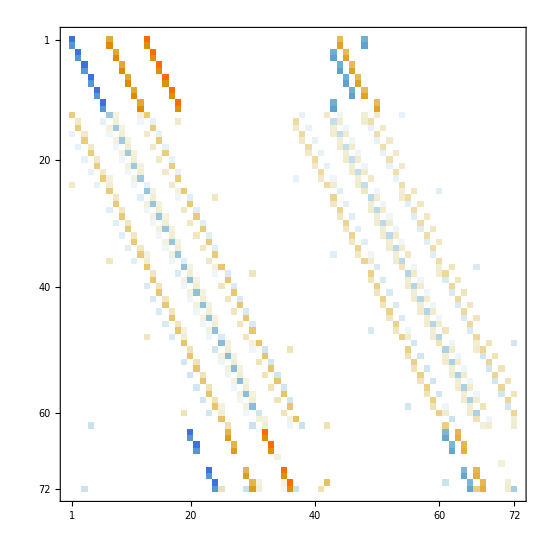

```mathematica
MatrixPlot[A]
```